# Testing out DMFormFactor functions

```mathematica
SetDirectory["/home/farmer/mathematica/DMFormFactor_13086288"]
```

/home/farmer/mathematica/DMFormFactor_13086288

```mathematica
<<"v6/dmformfactor-V6.m";
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

## Event rate

Model setup

```mathematica
(* Model Setup *)
SetJChi[1/2](* WIMP spin *)5645747356463
SetMChi[500 GeV] (* WIMP mass in GeV *)
dmfilename="default";  (* nuclear density matrix (using default density matrices) *)
bFM="default"; (* oscillation parameter (default: approximate formulae used) *)
IsotopeA=131;
SetIsotope[54,IsotopeA,bFM,dmfilename] (*[Z,A,bFM,filename]*)
ZeroCoeffs[];(*Reset all coefficients*)
SetCoeffsNonrel[1,c7,"p"]
SetCoeffsNonrel[1,c7,"n"]
(* Set non-zero NR EFT coefficient values *)
```

Getting default matrix...

Setting isotope to xenon-131.

```mathematica
(* Parameters *)
mNucleon=0.938 GeV;
NT=1/(IsotopeA* mNucleon);(*Number of target nuclei per detector mass*)
Centimeter=(10^13 Femtometer);
rhoDM=0.3GeV/Centimeter^3;(*Local dark matter density*)
ve=232 KilometerPerSecond;(*Earth's velocity in galactic rest frame*)
v0=220 KilometerPerSecond;(*Mean WIMP speed in galactic rest frame*)
vesc=550 KilometerPerSecond;
SetHalo["MBcutoff"];
```

```mathematica
dRdE=EventRate[NT,rhoDM,qGeV,ve,v0,vesc]; (* as function of q, not ER *)
```

Your Lagrangian is

L_prot=0.+(0.0000164977 1 c7)/GeV^2

L_neut=0.+(0.0000164977 1 c7)/GeV^2

Your event rate is

Recoil spectra for 150 GeV WIMP, for one coupling at a time (coupling values still set to 1)
Note units of (d R_D)/(d E_R) are “event rate per unit time, per unit detector mass, per unit recoil energy”

Note: E_R = q^2 / 2mT
i.e. q = sqrt( 2*mT*E_R )

Note units of (d R_D)/(d E_R) are “event rate per unit time, per unit detector mass, per unit recoil energy”. Multiplying in the exposure in kilogram days gets “event rate per unit recoil energy”
Note also kinematic threshold E_(R,max)=2(μ_T^2 v^2)/m_T, with μ_T=(m_χ m_T)/(m_χ+m_T)(I assume).

```mathematica
dRdE//Simplify
```

-1/GeV3.73328×10^-41 c7^2 ⅇ^(-67.4762 qGeV^2) (1.46049×10^-8-1.96592×10^-6 qGeV^2+0.000104387 qGeV^4-0.00284409 qGeV^6+0.0439191 qGeV^8-0.399075 qGeV^10+2.12932 qGeV^12-6.37604 qGeV^14+9.53564 qGeV^16-5.39718 qGeV^18+1. qGeV^20) ((0.13215-0.91619 qGeV^2-4.18132 Erf[1.05455-6.90607 qGeV]-4.18132 Erf[1.05455+6.90607 qGeV]) UnitStep[1.44545-6.90607 qGeV]+(-3.9959-0.386083 qGeV-0.458095 qGeV^2+1. qGeV^3-4.18132 Erf[1.05455-6.90607 qGeV]) UnitStep[3.55455-6.90607 qGeV,-1.44545+6.90607 qGeV])

```mathematica
(* Grid *)
mχ=500;(*GeV*)
mT = IsotopeA*mNucleon;
μT=(mχ GeV mT)/(mχ GeV+mT)
ERmax =2(μT^2 v^2)/mT/GeV/.v->ve(*just using earth speed to get rough number, and get rid of GeV units for plotting*)
ERmaxesc =2(μT^2 v^2)/mT/GeV/.v->vesc
```

98.6373 GeV

0.0000948336

0.000532981

```mathematica
dRdE/.c1->1
```

1/GeV 2.08424×10^-52 (0.+646.112 ⅇ^(-67.4762 qGeV^2) (0.+0.000958441 (2915.98-354651. qGeV^2+1.66663×10^7 qGeV^4-3.89909×10^8 qGeV^6+4.97028×10^9 qGeV^8-3.52778×10^10 qGeV^10+1.35444×10^11 qGeV^12-2.55168×10^11 qGeV^14+1.83904×10^11 qGeV^16-134154. qGeV^18+0.0248999 qGeV^20)+0.00191688 (4157.7-551594. qGeV^2+2.86787×10^7 qGeV^4-7.57984×10^8 qGeV^6+1.12026×10^10 qGeV^8-9.54998×10^10 qGeV^10+4.63347×10^11 qGeV^12-1.19651×10^12 qGeV^14+1.39184×10^12 qGeV^16-4.64714×10^11 qGeV^18+170015. qGeV^20)+0.000958441 (5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20)) (Erf[1.05455-6.90607 qGeV]+Erf[1.05455+6.90607 qGeV]))

```mathematica
Plot[10^-6*7800KilogramDay*dRdE GeV/.c1->1/.qGeV->√(10^-6*2mT ER/GeV),{ER,0,600},PlotRange->All]
```

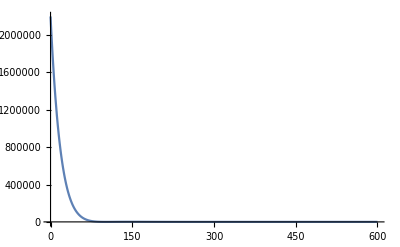

```mathematica
Plot[10^-6*7800KilogramDay*dRdE GeV/.c1->1/.qGeV->√(10^-6*2mT ER/GeV),{ER,0,600},PlotRange->All]
```